# Figure 2：vector–vector 模型中 g₂ 的计算（默认 g₂ = 1）

## 极点宽度、四条事件率曲线与零宽度对照

操作：将本笔记本、figure2_engine.wl 和 dmformfactor-V6.m 放在同一文件夹。用 Mathematica 打开后从头依次运行每个输入单元（Shift+Enter），或选择 Evaluation → Evaluate Notebook。两套曲线分别重新积分，完整运行可能需要数分钟。编辑参数后应从头重新计算。

本笔记本采用原稿 A. vector–vector 模型：V 与暗费米子非对角矢量流及核子矢量流相互作用；g₂ 是非对角标量 s 顶点的耦合。标量耦合的存在不代表换用了 scalar–pseudoscalar 模型。

## 一、物理输入（先在这里修改数值）

本节按标注的单位输入。数值程序统一使用 GeV；单位换算集中在后面的宽度计算和求解步骤。

### 1.1 粒子质量与耦合

三个耦合均无量纲。数值由下面输入单元指定。核子耦合采用质子和中子相同的约定；原稿中普适夸克耦合 gVq=gVN/3，因此由 gVN 推出。

```mathematica
(* 暗物质 chi1 和矢量媒介 V 的质量，单位 GeV。 *)
darkMatterMassGeV = 1000.;
mediatorMassGeV = 10.;

(* 暗费米子与矢量媒介的非对角耦合。 *)
g1val = 1.0;

(* 暗费米子与标量 s 的非对角耦合。 *)
g2val = 1.0;

(* 矢量媒介与单个核子的耦合，取质子与中子相同。 *)
gVNval = 1.0;

(* 原稿的普适夸克耦合和截面前因子均由上述输入推导。 *)
gVqval = gVNval/3;
couplingProductSquared = Abs[g1val * g2val * gVNval]^2;

Print["gVq = ", gVqval];
Print["|g1 g2 gVN|^2 = ", couplingProductSquared];
```

"gVq = "0.3333333333333333
"|g1 g2 gVN|^2 = "1.

### 1.2 四组质量组合

每行依次填写标量质量 ms（keV）和暗费米子质量劈裂 Δm（MeV）。宽度表、事件率和图例均读取这张表。第三、四行的 keV 输入沿用对原图图例的条件性解释。

```mathematica
benchmarks = {
  {200.,  1.},   (* 第 1 组 *)
  {300.,  1.},   (* 第 2 组 *)
  {360.,  1.},   (* 第 3 组 *)
  {300., 10.}    (* 第 4 组 *)
};
```

### 1.3 暗物质晕与氙靶

```mathematica
(* 局域暗物质密度，单位 GeV/cm.b3。 *)
localDensityGeVPerCm3 = 0.3;

(* 晕速度尺度、地球速度及逃逸速度，单位 km/s。 *)
haloSpeedScaleKmPerS = 220.;
earthSpeedKmPerS = 232.;
escapeSpeedKmPerS = 544.;

(* 天然氙摩尔质量，单位 g/mol。每个箭头右侧是数目丰度。 *)
xenonMolarMassGPerMol = 131.293;
abundances = <|
  128 -> 0.019102,
  129 -> 0.264006,
  130 -> 0.040710,
  131 -> 0.212324,
  132 -> 0.269086,
  134 -> 0.104357,
  136 -> 0.088573
|>;
isotopes = Keys[abundances];
```

### 1.4 固定速度微分截面的检查点

先指定同位素、质量组合、反冲能量和入射速度。运行下面的截面计算后，可以逐项检查核响应、三体积分、前因子和最终截面。

```mathematica
(* 固定速度微分截面的示例输入。 *)
diagnosticIsotope = 131;             (* 氙同位素的质量数 A *)
diagnosticBenchmarkIndex = 2;       (* 选用 1.2 节中的第几组 ms、Delta m *)
diagnosticRecoilKeV = 200.;          (* 核反冲能量 ER，单位 keV *)
diagnosticSpeedKmPerS = 776.;       (* 入射暗物质速度，单位 km/s *)
diagnosticWidthMode = "pole";        (* "pole" 极点宽度，"zero" 零宽度 *)
```

## 二、数值设置

```mathematica
(* 三体积分求积阶数，依次对应 W.b2、极角余弦、方位角。 *)
phaseSpaceOrders = {6, 6, 4};
speedOrder = 6;       (* 晕速度积分阶数 *)

(* 反冲能量网格，单位 keV。 *)
recoilMinKeV = 10.;
recoilMaxKeV = 800.;
recoilStepKeV = 10.;
extraRecoilEnergiesKeV = {101., 267., 542.};

(* 这些能量自动加入计算网格，并输出到对照表。 *)
comparisonEnergiesKeV = {200., 300., 542.};

(* 收敛检查使用质量表中的第几行，以及哪个反冲能量。 *)
convergenceBenchmarkIndex = 2;
convergenceRecoilKeV = 200.;
finePhaseSpaceOrders = {10, 10, 6};
fineSpeedOrder = 10;
```

## 三、模型、程序与派生量

### 3.1 物理约定

这里把 chi1、chi2 当作 Dirac 费米子，把 s 当作实标量，并假设 chi2 → chi1 s 是唯一开放衰变道，因而用这一分宽作为总宽。mchi2=mchi1+Delta m，采用纯标量 Yukawa 耦合 g₂ s bar(chi2) chi1 + h.c.。如果实际粒子类型、顶点或其他衰变道不同，须重算宽度。

宽度公式为 Gamma = |g₂|.b2 sqrt(Delta m.b2-ms.b2) [(2 mchi1+Delta m).b2-ms.b2]^(3/2) / [16 pi (mchi1+Delta m).b3]；Delta m≤ms 时该衰变道关闭。masses 统一用 GeV；公式写成分解形式以降低数值消减。

遵循原稿的固定极点宽度方案：标量在交换之后发射的传播子分母使用 W.b2-mchi2.b2+i mchi2 Gamma，另一张图保持原稿中的无宽度形式；两图先相加再做自旋迹。程序仍要求 Wmax < mchi2，不将上壳区域当成普通离壳散射。该 Breit–Wigner 处方是固定宽度近似，不是完整动量依赖一圈费米子自能。

零宽度和极点宽度计算使用同一组 g₁、g₂、gVN。g₂ 同时进入截面前因子和 χ₂ 的极点宽度，后者仅在极点宽度处方中使用。mV=10 GeV 是演示输入。

核反冲微分截面（原稿 radiative-recoil 公式）

(d σ_A)/(d E_R)=(m_A(g_1 g_2 g_VN)^2 ℛ_A(E_R))/(256 π^3 p_χ_1^2(m_V^2+2 m_A E_R)^2)
×∫_(W_min^2)^(W_max^2) d W^2 √(λ(W^2,m_χ_1^2,m_s^2)) ∫_-1^1 dz ⟨ℒ_00⟩_(φ_*)

式中 mA 是靶核质量，pχ₁ 是入射暗物质动量，ℛA 是相干核响应。λ 是原稿定义的无量纲相空间函数，W.b2 为 χ₁s 系统的不变质量平方，z 为标量发射极角余弦。角括号表示对方位角 φ* 取平均。程序 I6 计算两个显式积分及方位角平均，Rate 再乘截面前因子并做晕速度积分。

### 3.2 加载 AFH 核响应

AFH 默认数据涵盖这里列出的七种同位素。丰度是天然数目份额，按输入值直接加权。

```mathematica
baseDir = NotebookDirectory[];
enginePath = FileNameJoin[{baseDir,"three_body_rate_engine.wl"}];
afhPath = FileNameJoin[{baseDir,"dmformfactor-V6.m"}];
If[!FileExistsQ[enginePath] || !FileExistsQ[afhPath],Print["ERROR: engine or AFH package missing."];Abort[]];
expectedHash="dc0742f1c50b0a478adab62f2ddef6c82978ee034c1f177e0ed917deab5dd372";
If[ToLowerCase[FileHash[afhPath,"SHA256","HexString"]]=!=expectedHash,Print["ERROR: unexpected AFH source hash."];Abort[]];
Get[enginePath];
Fig2`LoadResponses[afhPath,isotopes];
Print["Version: ",$Version,"; AFH source SHA-256 verified."]
```

Style["Welcome to DMFormFactor version 1.1.", 32, RGBColor[0, 0, 1]]
"Functions are SetCoeffsNonrel, SetCoeffsRel, SetCoeffsNucl, ZeroCoeffs, SetJChi, SetMchi, SetIsotope, SetHALO, SetHelm, TransitionProbability, ResponseNucl, DiffCrossSection, ApproxTotalCrossSection, and EventRate."
"Getting default matrix..."
"Setting isotope to xenon-128."
"Getting default matrix..."
"Setting isotope to xenon-129."
"Getting default matrix..."
"Setting isotope to xenon-130."
"Getting default matrix..."
"Setting isotope to xenon-131."
"Getting default matrix..."
"Setting isotope to xenon-132."
"Getting default matrix..."
"Setting isotope to xenon-134."
"Getting default matrix..."
"Setting isotope to xenon-136."
"Version: ""14.2.0 for Microsoft Windows (64-bit) (December 26, 2024)""; AFH source SHA-256 verified."

### 3.3 将物理输入传给数值程序

下面的关联表把有单位的物理变量对应到求解器参数名。两套计算共用同一组输入，通过 widthMode 选择传播子处方。

```mathematica
parameters = <|
  "mchi"       -> darkMatterMassGeV,
  "mV"         -> mediatorMassGeV,
  "g2"         -> g2val,
  "couplingSq" -> couplingProductSquared,
  "rho"        -> localDensityGeVPerCm3,
  "v0"         -> haloSpeedScaleKmPerS,
  "vEarth"     -> earthSpeedKmPerS,
  "vEsc"       -> escapeSpeedKmPerS,
  "molarMass"  -> xenonMolarMassGPerMol,
  "isotopes"   -> isotopes,
  "abundance"  -> abundances,
  "quad"       -> phaseSpaceOrders,
  "nv"         -> speedOrder
|>;

pZero = Append[parameters, "widthMode" -> "zero"];
pPole = Append[parameters, "widthMode" -> "pole"];
```

### 3.4 计算各组极点宽度

```mathematica
(* 输入的质量先换算为 GeV，宽度结果再换回 keV。 *)
keVToGeV = 10^-6;
megaElectronVoltToGeV = 10^-3;
gevToKeV = 10^6;

poleWidthRow[{scalarMassKeV_, massSplittingMeV_}] := Module[
  {scalarMassGeV, massSplittingGeV, widthGeV},
  scalarMassGeV = scalarMassKeV * keVToGeV;
  massSplittingGeV = massSplittingMeV * megaElectronVoltToGeV;

  widthGeV = Fig2`Chi2Width[
    darkMatterMassGeV,
    scalarMassGeV,
    massSplittingGeV,
    g2val
  ];

  {scalarMassKeV, massSplittingMeV, widthGeV * gevToKeV}
];

widthTable = poleWidthRow /@ benchmarks;
Print["Included isotope abundance: ", Total[Values[abundances]]];
Print["g2 = ", g2val];

Grid[
  Prepend[widthTable, {"ms [keV]", "Delta m [MeV]", "Pole width [keV]"}],
  Frame -> All
]
```

"Included isotope abundance: "0.9981580000000001
"g2 = "1.

ms [keV] | Delta m [MeV] | Pole width [keV]
200. | 1. | 155.939
300. | 1. | 151.824
360. | 1. | 148.484
300. | 10. | 1590.81

### 3.5 实际计算固定速度微分截面

其中三体相空间积分 I6 对应下式，角括号内是包含两张图及干涉项的自旋迹。

I_6=∫_(W_min^2)^(W_max^2) d W^2 √(λ(W^2,m_χ_1^2,m_s^2)) ∫_-1^1 dz ⟨ℒ_00⟩_(φ_*)

其中 λ 为无量纲相空间函数，定义如下。

λ(W^2,m_χ_1^2,m_s^2)=[1-(m_χ_1+m_s)^2/W^2] [1-(m_χ_1-m_s)^2/W^2]

下列输入单元分别计算运动学、三体积分和截面前因子。表格中的结果基于第一节保存的输入；修改任何输入后，请从头运行所有单元以更新结果。质量使用 GeV，速度换算为 v/c。

```mathematica
(* AME2020 neutral-atom masses, converted to bare nuclear masses. *)
(* M_nucleus = (M_atom - Z m_e) u + B_e(Z); masses are GeV. *)
Global`ame2020XenonAtomicMassU = <|
  124 -> 123905885174/10^9, 126 -> 125904297422/10^9,
  128 -> 12790353075341/10^11, 129 -> 12890478085742/10^11,
  130 -> 129903509346/10^9, 131 -> 13090508412808/10^11,
  132 -> 13190415508346/10^11, 134 -> 133905393030/10^9,
  136 -> 135907214474/10^9 |>;
Global`xenonZ = 54;
Global`xenonAtomicMassUnitGeV = 93149410372/10^11; (* CODATA 2022 *)
Global`electronMassU = 5485799090441/10^16; (* CODATA 2022 *)
Global`xenonElectronBindingEnergyGeV =
  N[(144381/10^4 Global`xenonZ^(239/100) +
      155468/10^11 Global`xenonZ^(535/100)) 10^-9, 30];
Global`xenonNuclearMassGeV[A_Integer] := Module[{mAtom},
  mAtom = Lookup[Global`ame2020XenonAtomicMassU, A, Null];
  If[mAtom === Null, Return[$Failed]];
  N[(mAtom - Global`xenonZ Global`electronMassU) Global`xenonAtomicMassUnitGeV +
    Global`xenonElectronBindingEnergyGeV, 20]
];
Print[Table[{A, Global`xenonNuclearMassGeV[A]},
  {A, {128,129,130,131,132,134,136}}]];

(* 从第一节选择同位素、质量组合、反冲能量和速度。 *)
If[!MemberQ[isotopes, diagnosticIsotope],
  Print["错误：请在 1.3 节的同位素表中加入所选同位素。"]; Abort[]];
If[!IntegerQ[diagnosticBenchmarkIndex] ||
   !Between[diagnosticBenchmarkIndex, {1, Length[benchmarks]}],
  Print["错误：质量组合序号超出 benchmarks 范围。"]; Abort[]];
If[!TrueQ[0 < diagnosticSpeedKmPerS < 299792.458] ||
   !TrueQ[diagnosticRecoilKeV >= 0],
  Print["错误：要求 0 < v < c 且 ER >= 0。"]; Abort[]];

diagnosticParameters = Switch[diagnosticWidthMode,
  "pole", pPole,
  "zero", pZero,
  _, Print["错误：宽度处方请选择 pole 或 zero。"]; Abort[]
];

selectedScalarMassGeV = benchmarks[[diagnosticBenchmarkIndex, 1]] * keVToGeV;
selectedSplittingGeV = benchmarks[[diagnosticBenchmarkIndex, 2]] * megaElectronVoltToGeV;
selectedNuclearMassGeV = Global`xenonNuclearMassGeV[diagnosticIsotope];
selectedRecoilGeV = diagnosticRecoilKeV * keVToGeV;
selectedBeta = diagnosticSpeedKmPerS / 299792.458;
selectedChiEnergyGeV = darkMatterMassGeV / Sqrt[1 - selectedBeta^2];
selectedChiMomentumGeV = selectedChiEnergyGeV * selectedBeta;
selectedQGeV = Sqrt[2 * selectedNuclearMassGeV * selectedRecoilGeV + selectedRecoilGeV^2];

(* 原稿中的不变质量积分上下限，单位 GeV.b2。 *)
selectedW2Min = (darkMatterMassGeV + selectedScalarMassGeV)^2;
selectedW2Max = darkMatterMassGeV^2 + 2 * selectedChiMomentumGeV * selectedQGeV -
  2 * (selectedChiEnergyGeV + selectedNuclearMassGeV) * selectedRecoilGeV;

Grid[{
  {"物理量", "数值", "单位"},
  {"A", diagnosticIsotope, "无量纲"},
  {"mA", selectedNuclearMassGeV, "GeV"},
  {"p chi1", selectedChiMomentumGeV, "GeV"},
  {"Wmin.b2", NumberForm[selectedW2Min, {16, 6}, ExponentFunction -> (Null &)], "GeV.b2"},
  {"Wmax.b2", NumberForm[selectedW2Max, {16, 6}, ExponentFunction -> (Null &)], "GeV.b2"},
  {"Wmax.b2 - Wmin.b2", selectedW2Max - selectedW2Min, "GeV.b2"},
  {"三体相空间", If[selectedW2Max > selectedW2Min, "打开", "关闭"], ""}
}, Frame -> All]
```

{{128, 119.1139931767113543454446533009076451531`20.}, {129, 120.0466517449457060733618533009076451531`20.}, {130, 120.9769614432751634288794533009076451531`20.}, {131, 121.9099224472173273462170533009076451531`20.}, {132, 122.8405511513517045582306533009076451531`20.}, {134, 124.7046924986944351333594533009076451531`20.}, {136, 126.5693773704806913050394533009076451531`20.}}

物理量 | 数值 | 单位
A | 131 | 无量纲
mA | 121.90992244721732735 | GeV
p chi1 | 2.58847 | GeV
Wmin.b2 | 1000000.600000 | GeV.b2
Wmax.b2 | 1000000.694435 | GeV.b2
Wmax.b2 - Wmin.b2 | 0.0944345 | GeV.b2
三体相空间 | 打开 |

I6 对 W.b2、z 和方位角进行数值积分，其中方位角权重已经包含平均因子 1/(2π)。AFH 的核响应采用所选同位素和当前反冲能量。

```mathematica
(* 计算极点宽度和 AFH 相干核响应 R_A。 *)
selectedWidthGeV = If[diagnosticWidthMode === "pole",
  Fig2`Chi2Width[darkMatterMassGeV, selectedScalarMassGeV, selectedSplittingGeV, g2val],
  0.
];
selectedNuclearResponse = Fig2`NuclearResponse[diagnosticIsotope, diagnosticRecoilKeV];

(* I6 = 积分 dW.b2 sqrt(lambda) 积分 dz <L00>_phi。
   Fig2`I6 使用 2 节中给定的三体积分阶数。 *)
selectedI6GeV2 = Fig2`I6[
  darkMatterMassGeV,
  selectedScalarMassGeV,
  selectedSplittingGeV,
  selectedNuclearMassGeV,
  selectedRecoilGeV,
  diagnosticSpeedKmPerS,
  phaseSpaceOrders,
  selectedWidthGeV
];

Grid[{
  {"物理量", "数值", "单位"},
  {"Gamma chi2", selectedWidthGeV * gevToKeV, "keV"},
  {"R_A(ER)", selectedNuclearResponse, "无量纲"},
  {"I6", selectedI6GeV2, "GeV.b2"}
}, Frame -> All]
```

物理量 | 数值 | 单位
Gamma chi2 | 151.824 | keV
R_A(ER) | 9.62844 | 无量纲
I6 | 863152. | GeV.b2

下面直接把刚得到的 R_A 和 I6 代入上方公式。最后一列对照独立调用的固定速度截面函数；事件率积分也使用该函数所属的同一截面实现。

```mathematica
(* 公式中的矢量传播子分母和不含 I6 的整体前因子。 *)
selectedMediatorDenominator =
  (mediatorMassGeV^2 + 2 * selectedNuclearMassGeV * selectedRecoilGeV)^2;
If[!TrueQ[selectedMediatorDenominator > 0],
  Print["错误：矢量传播子分母为零。"]; Abort[]];

selectedPrefactorGeVMinus5 =
  selectedNuclearMassGeV * couplingProductSquared * selectedNuclearResponse /
  (256 * Pi^3 * selectedChiMomentumGeV^2 * selectedMediatorDenominator);

(* 把两重积分乘回前因子，得到 d sigma_A / d ER。 *)
selectedDSigmaGeVMinus3 = selectedPrefactorGeVMinus5 * selectedI6GeV2;
gevMinus2ToCm2 = 0.3893793721 * 10^-27;
selectedDSigmaCm2PerKeV = selectedDSigmaGeVMinus3 * gevMinus2ToCm2 * 10^-6;

(* 用供后续事件率调用的截面接口复核相同输入。 *)
selectedDSigmaCheck = Fig2`DifferentialCrossSection[
  diagnosticIsotope, diagnosticRecoilKeV, diagnosticSpeedKmPerS,
  selectedScalarMassGeV, selectedSplittingGeV, diagnosticParameters
];
selectedRelativeDifference = If[selectedDSigmaGeVMinus3 != 0,
  selectedDSigmaCheck / selectedDSigmaGeVMinus3 - 1,
  If[selectedDSigmaCheck == 0, 0, Indeterminate]
];

Grid[{
  {"物理量", "数值", "单位"},
  {"截面前因子", selectedPrefactorGeVMinus5, "GeV^-5"},
  {"d sigma / d ER", selectedDSigmaGeVMinus3, "GeV^-3"},
  {"d sigma / d ER", selectedDSigmaCm2PerKeV, "cm.b2/keV"},
  {"接口核对相对差", selectedRelativeDifference, "无量纲"}
}, Frame -> All]
```

物理量 | 数值 | 单位
截面前因子 | 2.20494×10^-6 | GeV^-5
d sigma / d ER | 1.9032 | GeV^-3
d sigma / d ER | 7.41067×10^-34 | cm.b2/keV
接口核对相对差 | -1.11022×10^-16 | 无量纲

使用第二节设置的较高积分阶数，对当前固定速度检查点重新计算 I6 与截面。该单点比较用于检查求积稳定性。

```mathematica
(* 增大 W.b2、极角和方位角的积分阶数后重新计算。 *)
selectedI6FineGeV2 = Fig2`I6[
  darkMatterMassGeV, selectedScalarMassGeV, selectedSplittingGeV,
  selectedNuclearMassGeV, selectedRecoilGeV, diagnosticSpeedKmPerS,
  finePhaseSpaceOrders, selectedWidthGeV
];
selectedDSigmaFine = selectedPrefactorGeVMinus5 * selectedI6FineGeV2;
selectedFineDifference = If[selectedDSigmaFine != 0,
  selectedDSigmaGeVMinus3 / selectedDSigmaFine - 1,
  If[selectedDSigmaGeVMinus3 == 0, 0, Indeterminate]
];
Grid[{
  {"积分阶数", "I6 [GeV.b2]", "d sigma/d ER [GeV^-3]"},
  {phaseSpaceOrders, selectedI6GeV2, selectedDSigmaGeVMinus3},
  {finePhaseSpaceOrders, selectedI6FineGeV2, selectedDSigmaFine},
  {"粗/细 - 1", "", selectedFineDifference}
}, Frame -> All]
```

积分阶数 | I6 [GeV.b2] | d sigma/d ER [GeV^-3]
{6,6,4} | 863152. | 1.9032
{10,10,6} | 862800. | 1.90242
粗/细 - 1 |  | 0.00040829

如果 Wmax.b2 不大于 Wmin.b2，I6 和截面为零。上述截面是在给定入射速度下针对一个同位素的计算；下一节的事件率再对晕速度分布积分并按同位素丰度加权。

### 3.6 固定速度微分截面曲线

下图使用第一节的同位素与入射速度，以及第二节的能量网格。每条曲线对应一组标量质量和质量劈裂，纵轴单位为 cm.b2/keV。

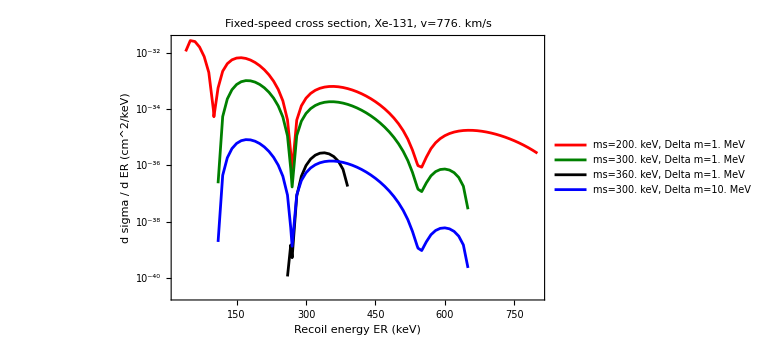

```mathematica
(* 使用第二节的反冲能量网格，并把额外检查点加入。 *)
fixedSpeedEnergyGridKeV = Sort[DeleteDuplicates[N[Join[
  Range[recoilMinKeV, recoilMaxKeV, recoilStepKeV],
  extraRecoilEnergiesKeV,
  comparisonEnergiesKeV
]]]];

(* 对每组质量逐点计算本节公式，结果保存为 {ER, d sigma/d ER}。 *)
fixedSpeedCrossSections = Table[
  Table[{
    recoilKeV,
    Fig2`DifferentialCrossSection[
      diagnosticIsotope, recoilKeV, diagnosticSpeedKmPerS,
      benchmark[[1]] * keVToGeV, benchmark[[2]] * megaElectronVoltToGeV,
      diagnosticParameters
    ] * gevMinus2ToCm2 * 10^-6
  }, {recoilKeV, fixedSpeedEnergyGridKeV}],
  {benchmark, benchmarks}
];

(* 对数坐标只绘制截面为正的点。 *)
positiveCrossSections = (Select[#, Last[#] > 0 &] &) /@ fixedSpeedCrossSections;
activeCrossSectionIndices = Select[Range[Length[benchmarks]],
  Length[positiveCrossSections[[#]]] > 0 &];

If[Length[activeCrossSectionIndices] == 0,
  Print["所选速度和能量范围内的截面均为零。"],
  fixedSpeedLabels = ("ms=" <> ToString[#[[1]]] <> " keV, Delta m=" <>
      ToString[#[[2]]] <> " MeV" &) /@ benchmarks;
  fixedSpeedPlot = ListLogPlot[
    positiveCrossSections[[activeCrossSectionIndices]],
    Joined -> True,
    PlotRange -> All,
    Frame -> True,
    (* 和后面的事件率图使用相同的基准颜色。 *)
    PlotStyle -> Table[
      {Red, RGBColor[0, .5, 0], Black, Blue}[[1 + Mod[index - 1, 4]]],
      {index, activeCrossSectionIndices}
    ],
    FrameLabel -> {"Recoil energy ER (keV)", "d sigma / d ER (cm^2/keV)"},
    PlotLegends -> Placed[fixedSpeedLabels[[activeCrossSectionIndices]], Below],
    PlotLabel -> "Fixed-speed cross section, Xe-" <> ToString[diagnosticIsotope] <>
      ", v=" <> ToString[diagnosticSpeedKmPerS] <> " km/s",
    ImageSize -> Large
  ];
  fixedSpeedPlot
]
```

AME2020 æ.9c.89é.99.90å®.bdå.ba.a6é.87.8dç®.97å·.b2å®.8cæ.88.90å.88°æ.9c¬è.8a.82å.9b.baå®.9aé.80.9få.ba.a6æ.88.aaé.9d¢æ.9b.b2ç.ba¿ï.bc.88ç¬¬ 13 ä¸.aaè.be.93å.85¥å.8d.95å.85.83ï.bc.89ã.80.82æ.9c¬è.8a.82å.90.8eç»æ.97§å.8d.95å.85.83å.90«é.9b¶å®.bdå.ba.a6å.af.b9ç.85§ï.bc.8cæ.9c¬æ¨¡å.9e.8bä¸.8dé.87.87ç.94¨è.af¥è¿.91ä.bc.bcï.bc.8cæ.95.85æ.9c.aaè¿.90è¡.8cï.bc.9bç.9b¸å.85.b3æ.97§è.be.93å.87.baå·.b2æ¸.85é.99¤ã.80.82

## 四、宽度与三体积分的代表点检验

这是固定的程序自检点，与第一节的作图输入独立。测试点 mchi=1000 GeV、mA=122 GeV、ms=300 keV、Delta m=1 MeV、ER=200 keV、v=776 km/s。对照值由独立 Python 程序在相同 Dirac 振幅、固定宽度处方与同一积分阶数下得到。

```mathematica
haloNorm=NIntegrate[Fig2`SpeedPDF[v,220.,232.,544.],{v,0,312,776}];
testWidth=Fig2`Chi2Width[1000.,0.0003,0.001,1.];
testZero=Fig2`I6[1000.,0.0003,0.001,122.,0.0002,776.,{16,16,8},0.];
testPole=Fig2`I6[1000.,0.0003,0.001,122.,0.0002,776.,{16,16,8},testWidth];
Grid[{{"check", "Mathematica", "reference"},
 {"halo integral",haloNorm,1.}, {"pole width [keV]",10^6 testWidth,151.8239115788},
 {"I6 zero [GeV^2]",testZero,878098.5567396},
 {"I6 g2=1 pole [GeV^2]",testPole,868246.7879206}},Frame->All]
```

```mathematica
If[Abs[haloNorm-1.]>10^-6 || Abs[testWidth/0.0001518239115787696-1]>10^-8 ||
 Abs[testZero/878098.5567396-1]>10^-6 || Abs[testPole/868246.7879206-1]>10^-6,
 Print["ERROR: diagnostic check failed."];Abort[],Print["PASS: independent benchmark checks."]]
```

## 五、分别计算零宽度和极点宽度曲线

曲线是单位曝光、单位核反冲能量的理论事件率，单位 events/(tonne year keV)，未加探测器效率、能量分辨率或背景。默认能量步长为 10 keV，并额外加入 101、267、542 keV，积分阶数为快速探索设置；用于论文应按下一节逐点检查收敛。

```mathematica
(* 将对照能量并入网格，方便修改起点、终点与步长。 *)
energies = Sort[DeleteDuplicates[N[Join[
  Range[recoilMinKeV, recoilMaxKeV, recoilStepKeV],
  extraRecoilEnergiesKeV,
  comparisonEnergiesKeV
]]]];
Print["Calculating zero-width reference ..."];
t0=AbsoluteTiming[curvesZero=Fig2`MakeCurves[energies,benchmarks,pZero];][[1]];
Print["Calculating g2=",g2val," fixed-pole-width curves ..."];
t1=AbsoluteTiming[curvesPole=Fig2`MakeCurves[energies,benchmarks,pPole];][[1]];
Print["Energy points: ",Length[energies],"; elapsed seconds: zero=",t0," pole=",t1]
```

## 六、绘图：实线是指定 g₂ 的极点宽度，虚线是零宽度

每个颜色对应同一组质量参数；同色实线与虚线只改变传播子宽度。两条线可能非常接近，可结合后面的比值图和数表查看差异。

```mathematica
(* 从质量表生成图例，修改质量组合时自动同步。 *)
baseColors = {Red, RGBColor[0,.5,0], Black, Blue};
colors = Table[baseColors[[1 + Mod[i - 1, Length[baseColors]]]],
  {i, Length[benchmarks]}];

benchmarkLabel[{scalarMassKeV_, massSplittingMeV_}] :=
  "ms=" <> ToString[scalarMassKeV] <> " keV, dm=" <>
  ToString[massSplittingMeV] <> " MeV";
labels = benchmarkLabel /@ benchmarks;

positiveZero=(Select[#,Last[#]>0&]&)/@curvesZero;
positivePole=(Select[#,Last[#]>0&]&)/@curvesPole;
stylesZero=Directive[#,Dashed,Opacity[.7]]&/@colors;
stylesPole=Directive[#,Thick]&/@colors;
ratePlot=ListLogPlot[Join[positivePole,positiveZero],Joined->True,
 PlotStyle->Join[stylesPole,stylesZero],PlotRange->All,Frame->True,
 FrameLabel->{"Recoil energy E_R (keV)","Rate [events/(tonne year keV)]"},
 PlotLegends->Placed[Join[(#<>"; pole"&)/@labels,(#<>"; zero"&)/@labels],Below],
 ImageSize->Large,PlotLabel->"Vector-vector model: fixed pole width vs zero-width reference"];
ratePlot
```

```mathematica
ratioCurves=Table[Select[MapThread[If[#1[[2]]>0 && #2[[2]]>0,{#1[[1]],#2[[2]]/#1[[2]]},Nothing]&,
 {curvesZero[[i]],curvesPole[[i]]}],ListQ],{i,Length[benchmarks]}];
ratioPlot=ListLinePlot[ratioCurves,Joined->True,PlotStyle->(Directive[#,Thick]&/@colors),
 PlotRange->All,Frame->True,FrameLabel->{"Recoil energy E_R (keV)","Pole width / zero-width rate"},
 PlotLegends->Placed[labels,Below],ImageSize->Large,
 PlotLabel->"Width sensitivity (points with zero reference omitted)"];
ratioPlot
```

## 七、代表能量逐项对照

零宽度事件率为零时，物理上该网格点相空间关闭或结果为零，此时不计算比例。300 keV benchmark 第一谷附近尤其应区分核响应谷值和运动学阈值。

```mathematica
energiesToCheck = N[comparisonEnergiesKeV];
compareRows=Flatten[Table[
 Module[{idx,zero,pole},idx=First@FirstPosition[energies,er];
  zero=curvesZero[[i,idx,2]];pole=curvesPole[[i,idx,2]];
  {i,er,zero,pole,If[zero>0,100 (pole/zero-1),"closed/zero"]}],
 {i,Length[benchmarks]},{er,energiesToCheck}],1];
Grid[Prepend[compareRows,{"benchmark","ER [keV]","zero width","g2="<>ToString[g2val]<>" pole width","change [%]"}],Frame->All]
```

## 八、独立数值收敛检查

按第二节指定的质量组合和反冲能量，比较两种宽度处方的粗细求积；这只是代表点，不保证所有曲线、谷底和阈值均收敛。请在重要的能量和 benchmark 处提高 quad、nv，再减小能量步长。

```mathematica
(* 收敛点和更细的积分阶数读取第二节的设置。 *)
{convergenceMsKeV, convergenceDeltaMMeV} =
  benchmarks[[convergenceBenchmarkIndex]];
convergenceMsGeV = convergenceMsKeV * keVToGeV;
convergenceDeltaMGeV = convergenceDeltaMMeV * megaElectronVoltToGeV;

fineOrders = <|"quad" -> finePhaseSpaceOrders, "nv" -> fineSpeedOrder|>;
pZeroFine = Join[pZero, fineOrders];
pPoleFine = Join[pPole, fineOrders];

coarse0 = Fig2`Rate[convergenceRecoilKeV, convergenceMsGeV, convergenceDeltaMGeV, pZero];
fine0 = Fig2`Rate[convergenceRecoilKeV, convergenceMsGeV, convergenceDeltaMGeV, pZeroFine];
coarse1 = Fig2`Rate[convergenceRecoilKeV, convergenceMsGeV, convergenceDeltaMGeV, pPole];
fine1 = Fig2`Rate[convergenceRecoilKeV, convergenceMsGeV, convergenceDeltaMGeV, pPoleFine];

relativeDifference[coarse_, fine_] :=
  If[fine > 0, coarse/fine - 1, "NA"];
Print["Convergence point: ", benchmarkLabel[benchmarks[[convergenceBenchmarkIndex]]],
  ", ER=", convergenceRecoilKeV, " keV"];
Grid[{{"width prescription","coarse","fine","coarse/fine-1"},
 {"zero width",coarse0,fine0,relativeDifference[coarse0, fine0]},
 {"pole width",coarse1,fine1,relativeDifference[coarse1, fine1]}},Frame->All]
```

## 九、可选：导出图像和数据

执行本单元才会写出图像与 CSV 到 g2_output；重复运行会覆盖同名文件。每条曲线保存能量、零宽度、极点宽度及两者比值。

```mathematica
outDir=FileNameJoin[{baseDir,"g2_output"}];If[!DirectoryQ[outDir],CreateDirectory[outDir]];
(* ASCII CSV: e notation, explicit quoting for strings; compatible with Excel/Python. *)
formatNumber[n_?NumericQ]:=StringReplace[StringReplace[ToString[InputForm[N[n]],CharacterEncoding->"ASCII"],
 RegularExpression["`[0-9.]*"]->""],"*^"->"e"];
formatField[s_String]:="\""<>StringReplace[s,"\""->"\"\""]<>"\"";
formatField[n_?NumericQ]:=formatNumber[n];
writeCSV[path_,rows_]:=Module[{stream=OpenWrite[path,CharacterEncoding->"ASCII"]},
 Scan[(WriteString[stream,StringRiffle[formatField/@#,","],"\n"])&,rows];Close[stream];path];
Do[writeCSV[FileNameJoin[{outDir,"benchmark_"<>ToString[i]<>"_g2_compare.csv"}],
 Prepend[MapThread[{#1[[1]],#1[[2]],#2[[2]],If[#1[[2]]>0,#2[[2]]/#1[[2]],"NA"]}&,
  {curvesZero[[i]],curvesPole[[i]]}],{"ER_keV","rate_zero","rate_pole","pole_over_zero"}]],{i,Length[benchmarks]}];
writeCSV[FileNameJoin[{outDir,"pole_widths.csv"}],Prepend[widthTable,{"ms_keV","delta_m_MeV","gamma_keV"}]];
writeCSV[FileNameJoin[{outDir,"selected_energies.csv"}],Prepend[compareRows,{"benchmark","ER_keV","rate_zero","rate_pole","change_percent"}]];
Export[FileNameJoin[{outDir,"rate_compare.png"}],ratePlot,"PNG",ImageResolution->180];
Export[FileNameJoin[{outDir,"ratio_compare.png"}],ratioPlot,"PNG",ImageResolution->180];
Print["Results exported to: ",outDir]
```

本笔记本输出的是给定近似和参数的理论预测，不能单独确定原图真实输入或实验事件数。固定极点宽度、离壳自能处理、Dirac/Majorana 约定、核响应与完整截面归一化均应单独审计。